{{24.9382,49.3734},{-124.759,-67.007}}

GeoGraphics::missloc: Unable to obtain location information for Great Lakes.

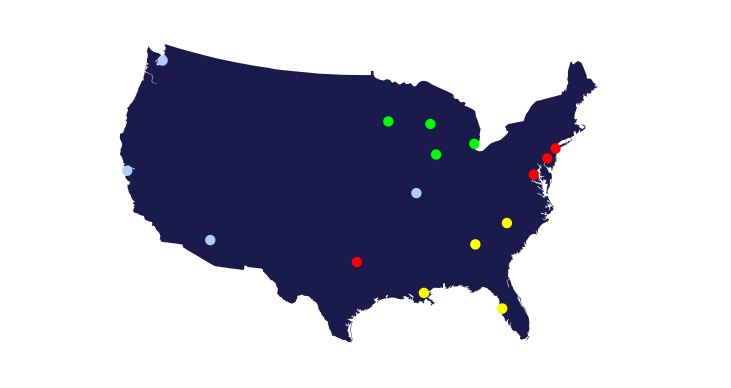

-Graphics-

```mathematica
bounds = GeoBounds[LinguisticAssistant]
GeoGraphics[{GeoStyling[RGBColor[.1,.1,.3], Opacity[1]],Polygon[LinguisticAssistant],GeoStyling[RGBColor[1,1,1], Opacity[1]],Polygon[], GeoStyling[Opacity[1]],nfcDisks}, GeoRange->bounds, GeoBackground->RGBColor[1, 1,1]]
GeoGraphics[{GeoStyling[Opacity[1]],nfcDisks}]
```

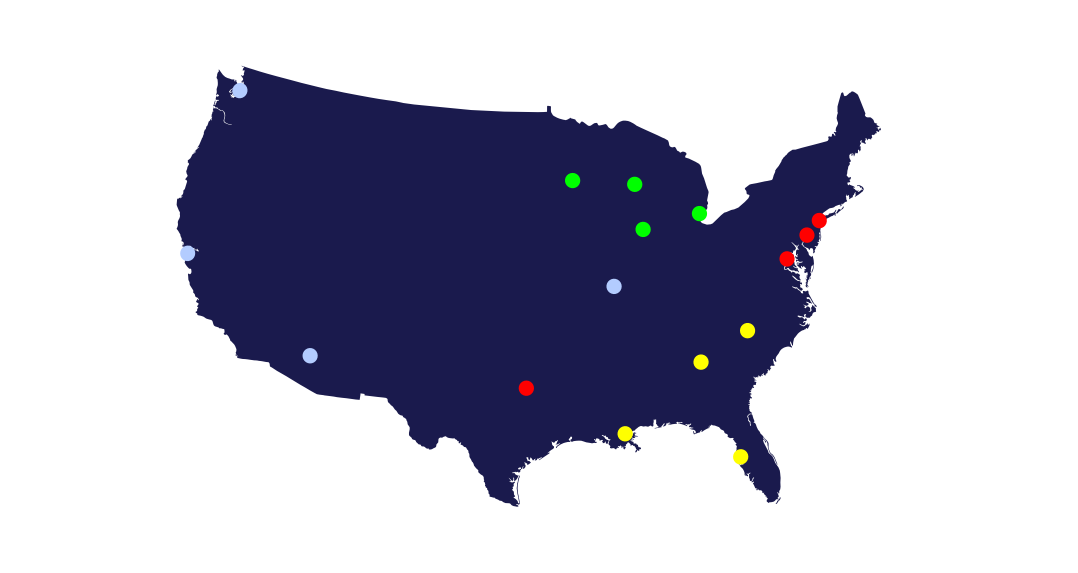

-Graphics-

```mathematica
nfcEastTeams = {Entity["City",{"NewYork","NewYork","UnitedStates"}], Entity["City",{"Philadelphia","Pennsylvania","UnitedStates"}], Entity["City",{"Washington","DistrictOfColumbia","UnitedStates"}], Entity["City",{"Dallas","Texas","UnitedStates"}]}

nfcNorthTeams = {Entity["City",{"GreenBay","Wisconsin","UnitedStates"}], Entity["City",{"Chicago","Illinois","UnitedStates"}], Entity["City",{"Detroit","Michigan","UnitedStates"}], Entity["City",{"SaintPaul","Minnesota","UnitedStates"}]}
nfcSouthTeams = {Entity["City",{"Charlotte","NorthCarolina","UnitedStates"}], Entity["City",{"Atlanta","Georgia","UnitedStates"}], Entity["City",{"NewOrleans","Louisiana","UnitedStates"}],Entity["City",{"Tampa","Florida","UnitedStates"}]} 
nfcWestTeams = {LinguisticAssistant, LinguisticAssistant, LinguisticAssistant, LinguisticAssistant}

nfcEast=Table[EntityValue[nfcEastTeams[[i]], "Position"], {i, 1, 4}]
nfcNorth = Table[EntityValue[nfcNorthTeams[[i]], "Position"], {i, 1, 4}]
nfcSouth =  Table[EntityValue[nfcSouthTeams[[i]], "Position"], {i, 1, 4}]
nfcWest =  Table[EntityValue[nfcWestTeams[[i]], "Position"], {i, 1, 4}]
nfc = {nfcEast, nfcNorth, nfcWest, nfcSouth}
```

{New York City,Philadelphia,Washington,Dallas}

{Green Bay,Chicago,Detroit,Saint Paul}

{Charlotte,Atlanta,New Orleans,Tampa}

{San Francisco,Seattle,Phoenix,Saint Louis}

{GeoPosition[{40.6643,-73.9385}],GeoPosition[{40.0094,-75.1333}],GeoPosition[{38.9041,-77.0171}],GeoPosition[{32.7942,-96.7655}]}

{GeoPosition[{44.5134,-88.0158}],GeoPosition[{41.8376,-87.6818}],GeoPosition[{42.383,-83.1022}],GeoPosition[{44.9489,-93.1039}]}

{GeoPosition[{35.2087,-80.8307}],GeoPosition[{33.7629,-84.4227}],GeoPosition[{29.9728,-90.059}],GeoPosition[{27.9701,-82.4797}]}

{GeoPosition[{37.7599,-122.437}],GeoPosition[{47.6205,-122.351}],GeoPosition[{33.5722,-112.088}],GeoPosition[{38.6357,-90.2446}]}

{{GeoPosition[{40.6643,-73.9385}],GeoPosition[{40.0094,-75.1333}],GeoPosition[{38.9041,-77.0171}],GeoPosition[{32.7942,-96.7655}]},{GeoPosition[{44.5134,-88.0158}],GeoPosition[{41.8376,-87.6818}],GeoPosition[{42.383,-83.1022}],GeoPosition[{44.9489,-93.1039}]},{GeoPosition[{37.7599,-122.437}],GeoPosition[{47.6205,-122.351}],GeoPosition[{33.5722,-112.088}],GeoPosition[{38.6357,-90.2446}]},{GeoPosition[{35.2087,-80.8307}],GeoPosition[{33.7629,-84.4227}],GeoPosition[{29.9728,-90.059}],GeoPosition[{27.9701,-82.4797}]}}

```mathematica
nfc = {nfcEast, nfcNorth, nfcWest, nfcSouth}
nfcColors= {Red, Green, RGBColor[.7,.8,1], Yellow}
r=Quantity[35, "Kilometers"];

nfcDisks = Table[{nfcColors[[i]],GeoDisk[nfc[[i,j]],r]}, {i,1,4}, {j,1,4}]
```

{{GeoPosition[{40.6643,-73.9385}],GeoPosition[{40.0094,-75.1333}],GeoPosition[{38.9041,-77.0171}],GeoPosition[{32.7942,-96.7655}]},{GeoPosition[{44.5134,-88.0158}],GeoPosition[{41.8376,-87.6818}],GeoPosition[{42.383,-83.1022}],GeoPosition[{44.9489,-93.1039}]},{GeoPosition[{37.7599,-122.437}],GeoPosition[{47.6205,-122.351}],GeoPosition[{33.5722,-112.088}],GeoPosition[{38.6357,-90.2446}]},{GeoPosition[{35.2087,-80.8307}],GeoPosition[{33.7629,-84.4227}],GeoPosition[{29.9728,-90.059}],GeoPosition[{27.9701,-82.4797}]}}

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0.7, 0.8, 1],RGBColor[1, 1, 0]}

{{{RGBColor[1, 0, 0],GeoDisk[GeoPosition[{40.6643,-73.9385}],35 km]},{RGBColor[1, 0, 0],GeoDisk[GeoPosition[{40.0094,-75.1333}],35 km]},{RGBColor[1, 0, 0],GeoDisk[GeoPosition[{38.9041,-77.0171}],35 km]},{RGBColor[1, 0, 0],GeoDisk[GeoPosition[{32.7942,-96.7655}],35 km]}},{{RGBColor[0, 1, 0],GeoDisk[GeoPosition[{44.5134,-88.0158}],35 km]},{RGBColor[0, 1, 0],GeoDisk[GeoPosition[{41.8376,-87.6818}],35 km]},{RGBColor[0, 1, 0],GeoDisk[GeoPosition[{42.383,-83.1022}],35 km]},{RGBColor[0, 1, 0],GeoDisk[GeoPosition[{44.9489,-93.1039}],35 km]}},{{RGBColor[0.7, 0.8, 1],GeoDisk[GeoPosition[{37.7599,-122.437}],35 km]},{RGBColor[0.7, 0.8, 1],GeoDisk[GeoPosition[{47.6205,-122.351}],35 km]},{RGBColor[0.7, 0.8, 1],GeoDisk[GeoPosition[{33.5722,-112.088}],35 km]},{RGBColor[0.7, 0.8, 1],GeoDisk[GeoPosition[{38.6357,-90.2446}],35 km]}},{{RGBColor[1, 1, 0],GeoDisk[GeoPosition[{35.2087,-80.8307}],35 km]},{RGBColor[1, 1, 0],GeoDisk[GeoPosition[{33.7629,-84.4227}],35 km]},{RGBColor[1, 1, 0],GeoDisk[GeoPosition[{29.9728,-90.059}],35 km]},{RGBColor[1, 1, 0],GeoDisk[GeoPosition[{27.9701,-82.4797}],35 km]}}}

```mathematica
GeoGraphics[{nfcDisks}]
```

-Graphics-

{{24.9382,49.3734},{-124.759,-67.007}}

GeoGraphics::missloc: Unable to obtain location information for Lake Michigan.

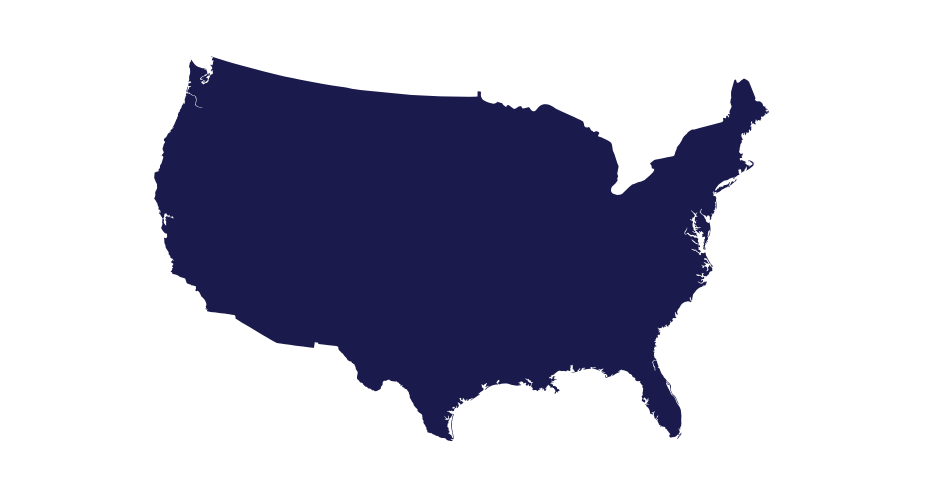

```mathematica
bounds = GeoBounds[LinguisticAssistant];
GeoGraphics[{GeoStyling[RGBColor[.1,.1,.3], Opacity[1]],Polygon[LinguisticAssistant],GeoStyling[White, Opacity[1]],Polygon[LinguisticAssistant]}, GeoRange->bounds, GeoBackground->White]
```

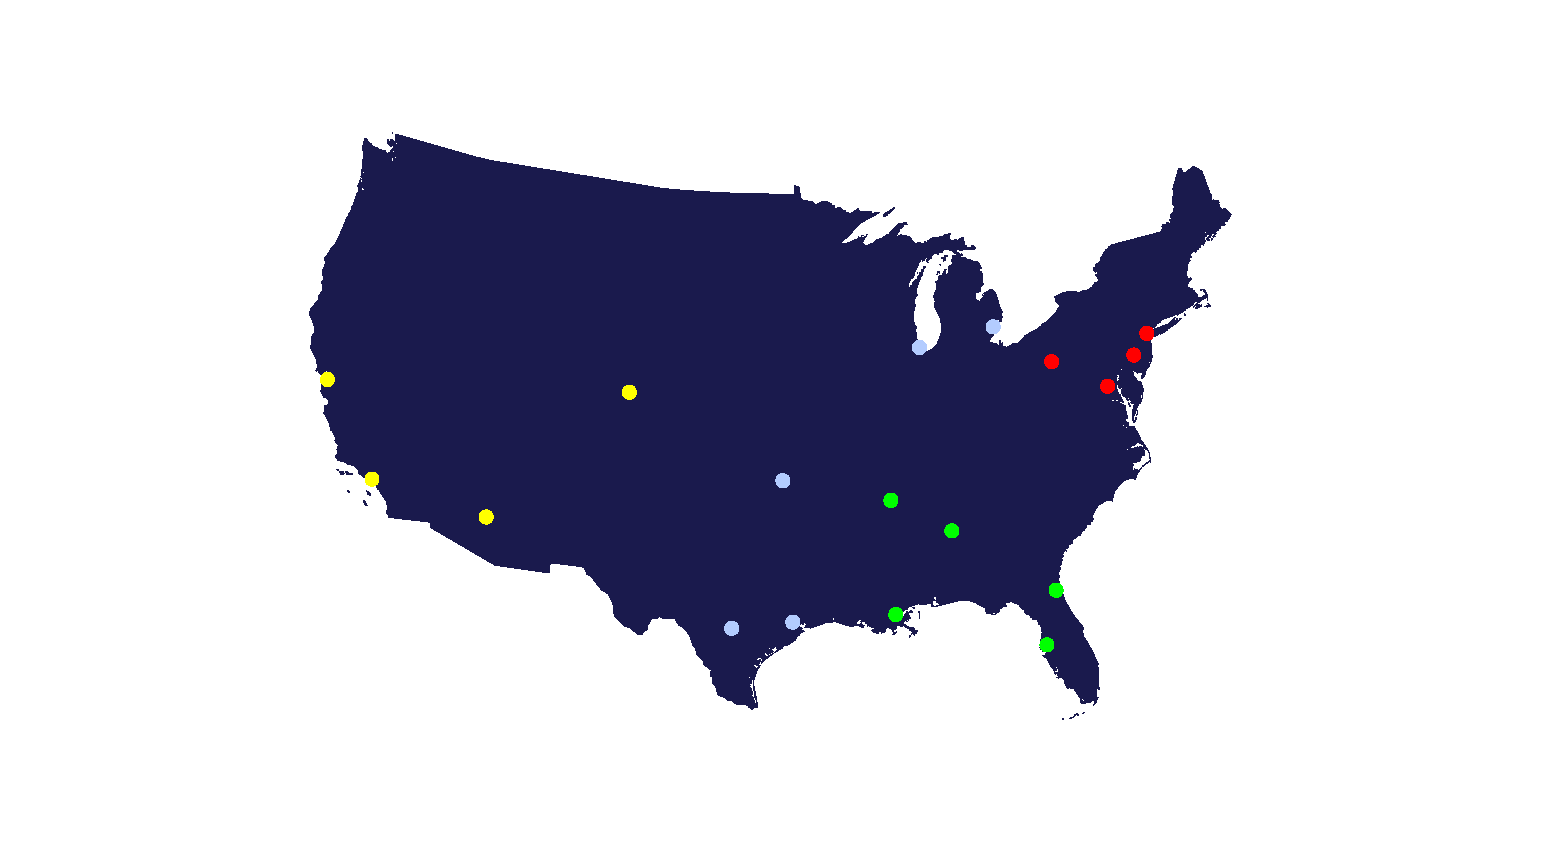

```mathematica
GeoGraphics[{GeoStyling[RGBColor[0.1,0.1,0.3],Opacity[1]],EntityClass["AdministrativeDivision","ContinentalUSStates"]["Polygon"], GeoStyling[Opacity[1]],usflDisks},GeoBackground->None]
```

```mathematica
usflAtlanticTeams = {LinguisticAssistant, LinguisticAssistant, LinguisticAssistant, LinguisticAssistant};
usflSouthernTeams ={LinguisticAssistant, LinguisticAssistant, LinguisticAssistant, LinguisticAssistant, LinguisticAssistant}
usflCentralTeams={LinguisticAssistant, LinguisticAssistant, LinguisticAssistant, LinguisticAssistant, LinguisticAssistant}
usflPacificTeams={LinguisticAssistant, LinguisticAssistant, LinguisticAssistant, LinguisticAssistant}
usflAtlantic=Table[EntityValue[usflAtlanticTeams[[i]], "Position"], {i, 1, 4}]
usflSouthern = Table[EntityValue[usflSouthernTeams[[i]], "Position"], {i, 1, 5}]
usflCentral=  Table[EntityValue[usflCentralTeams[[i]], "Position"], {i, 1, 5}]
usflPacific =  Table[EntityValue[usflPacificTeams[[i]], "Position"], {i, 1, 4}]
usfl1984 = {usflAtlantic, usflSouthern, usflCentral, usflPacific}
```

{Birmingham,Tampa,New Orleans,Memphis,Jacksonville}

{Houston,Detroit,San Antonio,Tulsa,Chicago}

{Los Angeles,Tempe,Denver,Oakland}

{GeoPosition[{40.0094,-75.1333}],GeoPosition[{40.8122,-74.0769}],GeoPosition[{40.4398,-79.9766}],GeoPosition[{38.9041,-77.0171}]}

{GeoPosition[{33.5274,-86.799}],GeoPosition[{27.9701,-82.4797}],GeoPosition[{29.9728,-90.059}],GeoPosition[{35.1035,-89.9785}],GeoPosition[{30.337,-81.6613}]}

{GeoPosition[{29.7805,-95.3863}],GeoPosition[{42.383,-83.1022}],GeoPosition[{29.4724,-98.5251}],GeoPosition[{36.1279,-95.9023}],GeoPosition[{41.8376,-87.6818}]}

{GeoPosition[{34.0194,-118.411}],GeoPosition[{33.3884,-111.932}],GeoPosition[{39.7618,-104.881}],GeoPosition[{37.7699,-122.226}]}

{{GeoPosition[{40.0094,-75.1333}],GeoPosition[{40.8122,-74.0769}],GeoPosition[{40.4398,-79.9766}],GeoPosition[{38.9041,-77.0171}]},{GeoPosition[{33.5274,-86.799}],GeoPosition[{27.9701,-82.4797}],GeoPosition[{29.9728,-90.059}],GeoPosition[{35.1035,-89.9785}],GeoPosition[{30.337,-81.6613}]},{GeoPosition[{29.7805,-95.3863}],GeoPosition[{42.383,-83.1022}],GeoPosition[{29.4724,-98.5251}],GeoPosition[{36.1279,-95.9023}],GeoPosition[{41.8376,-87.6818}]},{GeoPosition[{34.0194,-118.411}],GeoPosition[{33.3884,-111.932}],GeoPosition[{39.7618,-104.881}],GeoPosition[{37.7699,-122.226}]}}

```mathematica
usflColors= {Red, Green, RGBColor[.7,.8,1], Yellow}
r=Quantity[35, "Kilometers"];

usflDisks = Table[{usflColors[[i]], GeoDisk[usfl1984[[i,j]],r]}, {i, 1, 4}, {j,1,Length[usfl1984[[i]]]}]
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0.7, 0.8, 1],RGBColor[1, 1, 0]}

{{{RGBColor[1, 0, 0],GeoDisk[GeoPosition[{40.0094,-75.1333}],35 km]},{RGBColor[1, 0, 0],GeoDisk[GeoPosition[{40.8122,-74.0769}],35 km]},{RGBColor[1, 0, 0],GeoDisk[GeoPosition[{40.4398,-79.9766}],35 km]},{RGBColor[1, 0, 0],GeoDisk[GeoPosition[{38.9041,-77.0171}],35 km]}},{{RGBColor[0, 1, 0],GeoDisk[GeoPosition[{33.5274,-86.799}],35 km]},{RGBColor[0, 1, 0],GeoDisk[GeoPosition[{27.9701,-82.4797}],35 km]},{RGBColor[0, 1, 0],GeoDisk[GeoPosition[{29.9728,-90.059}],35 km]},{RGBColor[0, 1, 0],GeoDisk[GeoPosition[{35.1035,-89.9785}],35 km]},{RGBColor[0, 1, 0],GeoDisk[GeoPosition[{30.337,-81.6613}],35 km]}},{{RGBColor[0.7, 0.8, 1],GeoDisk[GeoPosition[{29.7805,-95.3863}],35 km]},{RGBColor[0.7, 0.8, 1],GeoDisk[GeoPosition[{42.383,-83.1022}],35 km]},{RGBColor[0.7, 0.8, 1],GeoDisk[GeoPosition[{29.4724,-98.5251}],35 km]},{RGBColor[0.7, 0.8, 1],GeoDisk[GeoPosition[{36.1279,-95.9023}],35 km]},{RGBColor[0.7, 0.8, 1],GeoDisk[GeoPosition[{41.8376,-87.6818}],35 km]}},{{RGBColor[1, 1, 0],GeoDisk[GeoPosition[{34.0194,-118.411}],35 km]},{RGBColor[1, 1, 0],GeoDisk[GeoPosition[{33.3884,-111.932}],35 km]},{RGBColor[1, 1, 0],GeoDisk[GeoPosition[{39.7618,-104.881}],35 km]},{RGBColor[1, 1, 0],GeoDisk[GeoPosition[{37.7699,-122.226}],35 km]}}}

```mathematica
Length[usfl1984[[4]]]

usfl1984
```

4

{{GeoPosition[{40.0094,-75.1333}],GeoPosition[{40.8122,-74.0769}],GeoPosition[{40.4398,-79.9766}],GeoPosition[{38.9041,-77.0171}]},{GeoPosition[{33.5274,-86.799}],GeoPosition[{27.9701,-82.4797}],GeoPosition[{29.9728,-90.059}],GeoPosition[{35.1035,-89.9785}]},{GeoPosition[{29.7805,-95.3863}],GeoPosition[{42.383,-83.1022}],GeoPosition[{29.4724,-98.5251}],GeoPosition[{36.1279,-95.9023}]},{GeoPosition[{34.0194,-118.411}],GeoPosition[{33.3884,-111.932}],GeoPosition[{39.7618,-104.881}],GeoPosition[{37.7699,-122.226}]}}